```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
PortfolioChart[stocks_,start_,end_]:=Module[{s,portfolio,data,symbols,std,return},
s=NormalizeData[#,start,end]&/@stocks;
portfolio=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{portfolio};
symbols=stocks~Join~{"portfolio"};
std=StandardDeviation@portfolio[[All,2]];
return=Last@portfolio[[All,2]];
{DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All],{return,std,return/std}//TableForm[#,TableHeadings->{{"return","std","r/s"},Automatic}]&}
]
RobustChart[symbols_,start_,end_]:=Module[{lists,datesPrices,dates,uniqueKeys,data,portfolio,numbers,std,return,ts},
lists=NormalizeData[#,start,end]&/@symbols;
datesPrices=Table[#1->#2&@@i,{stock,lists},{i,stock}];
dates=Table[#1&@@i,{stock,lists},{i,stock}];
uniqueKeys=Fold[Union,dates];
data=Table[Module[{association},
association=Association@d;
Table[i->association[i],{i,uniqueKeys}]],{d,datesPrices}];
portfolio=Normal@Merge[data,Mean];
numbers=Select[portfolio[[All,2]],NumberQ];
std=StandardDeviation@numbers//N;
return=Last@numbers//N;
ts=Transpose@{Keys@#,Values@#}&/@(data~Join~{portfolio});
{DateListPlot[ts,PlotLegends->symbols~Join~{"Mean"},PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All],{return,std,return/std}//TableForm[#,TableHeadings->{{"return","std","r/s"},Automatic}]&}
]
```

```mathematica
start=DatePlus[Today,-Quantity[5, "Years"]];
start1=DatePlus[Today,-Quantity[1, "Years"]];
start2=DatePlus[Today,-Quantity[2, "Years"]];
end=Today;
end//DateString
```

Sat 28 Jul 2018

```mathematica
symbols={"AMZN","MSFT","V","BA","MA","JPM","CSCO","INTC","NFLX","ADBE"};
RobustChart[symbols,start,end]//Export[FileNameJoin[{NotebookDirectory[],"portfolio10.pdf"}],#]&;
RobustChart[{"AMZN","MSFT","V","MA","NFLX","ADBE"},start,end]//Export[FileNameJoin[{NotebookDirectory[],"portfolio6.pdf"}],#]&;
```

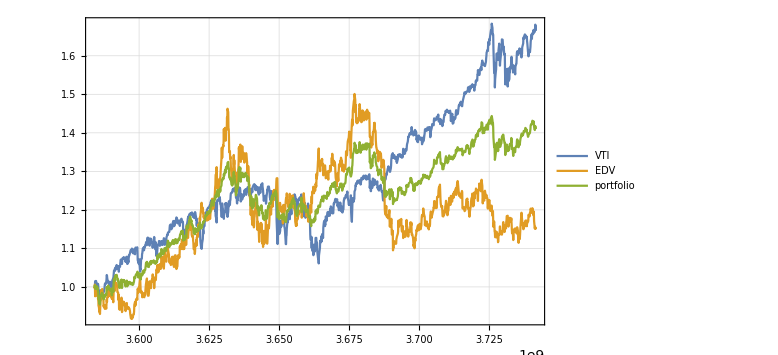
{-Graphics-,return | 1.40959
std | 0.119416
r/s | 11.804}

```mathematica
PortfolioChart[{"VTI","EDV"},start,end]
```

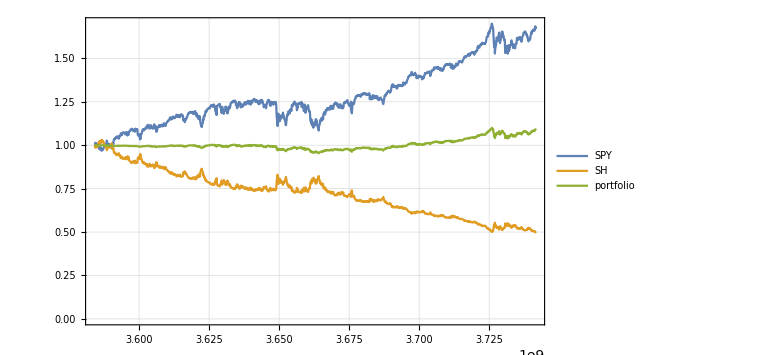
{-Graphics-,return | 1.08623
std | 0.0297337
r/s | 36.5319}

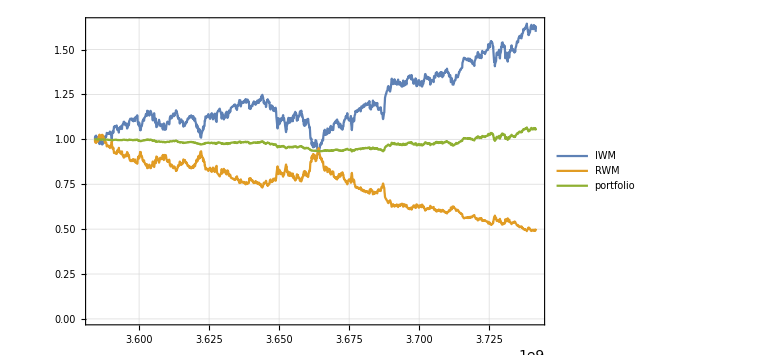
{-Graphics-,return | 1.05005
std | 0.0269165
r/s | 39.0115}

```mathematica
PortfolioChart[{"SPY","SH"},start,end]
PortfolioChart[{"IWM","RWM"},start,end]
```

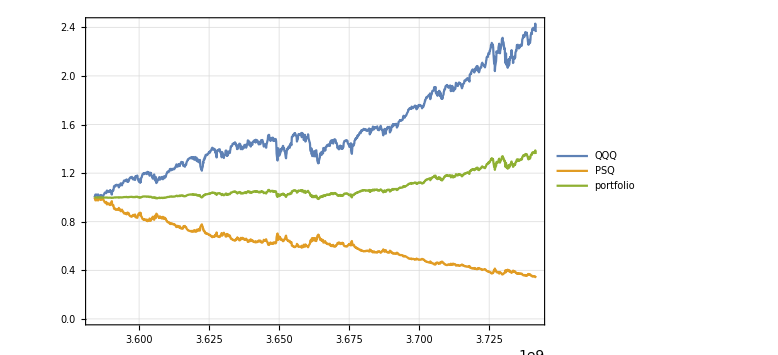
{-Graphics-,return | 1.35735
std | 0.100294
r/s | 13.5336}

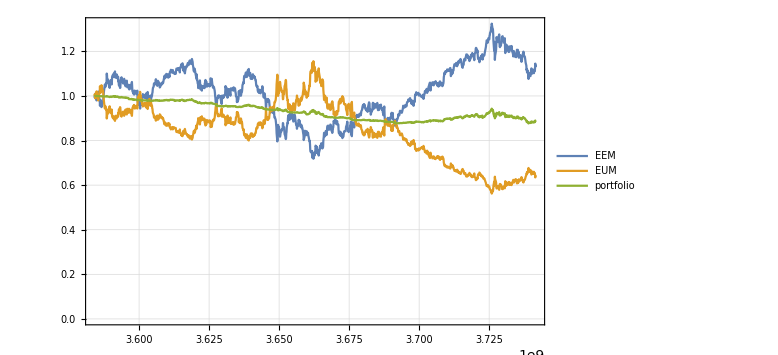
{-Graphics-,return | 0.888086
std | 0.0384401
r/s | 23.1031}

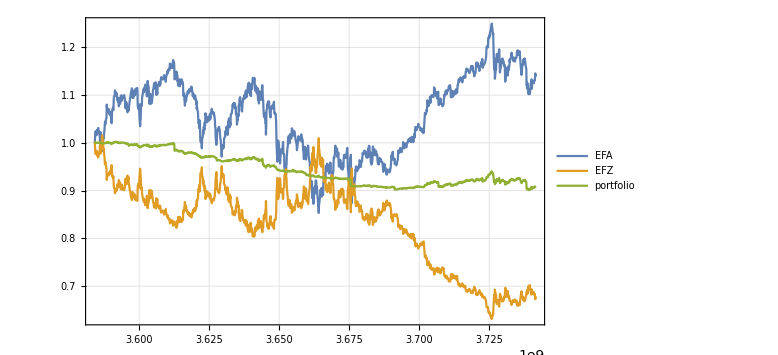
{-Graphics-,return | 0.909123
std | 0.0331784
r/s | 27.4011}

```mathematica
PortfolioChart[{"QQQ","PSQ"},start,end]
PortfolioChart[{"EEM","EUM"},start,end]
PortfolioChart[{"EFA","EFZ"},start,end]
```

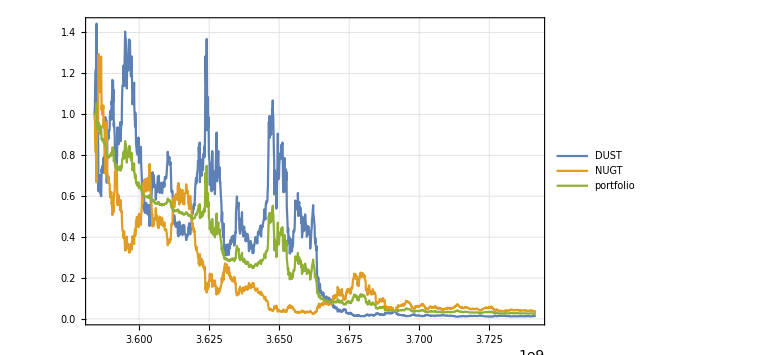
{-Graphics-,return | 0.0247696
std | 0.264988
r/s | 0.0934745}

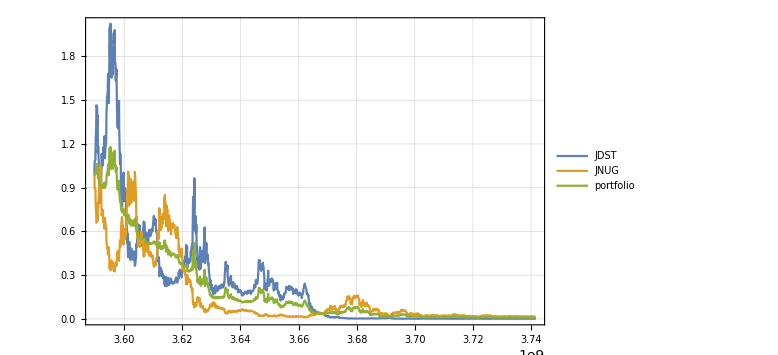
{-Graphics-,return | 0.00874565
std | 0.270416
r/s | 0.0323415}

```mathematica
PortfolioChart[{"DUST","NUGT"},start,end]
PortfolioChart[{"JDST","JNUG"},start,end]
```